i::shdw: Symbol "i" appears in multiple contexts {"AffinityPropagation3`", "Global`"}; definitions in context "AffinityPropagation3`" may shadow or be shadowed by other definitions.

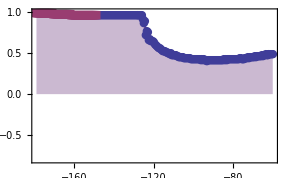

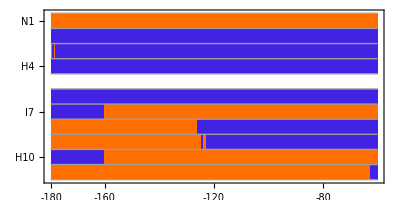
-Graphics-ξ [degrees]

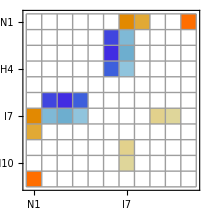

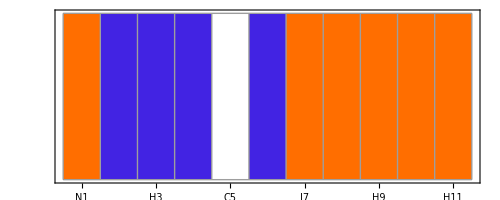
-Graphics-SCORE = 0.979

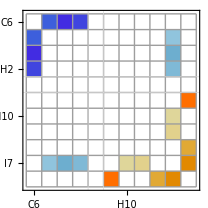

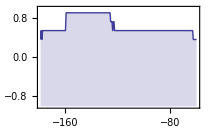

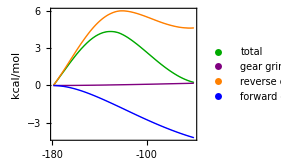

```mathematica
(*
WNIOSKI:
143.37801
137.19448
131.12541




*)
Needs["AffinityPropagation3`","affinityPropagationPackage3.m"];
Needs["SpectralClustering`","spectralClusteringPackage.m"];
Needs["ErrorBarPlots`"]


score1[clustering_,mat_]:=Module[{tmp,flatMat,which,plusMat,minusMat,gravityScore,clarityScore,flatMutualMat,totalPlus,totalMinus},

flatMat=Flatten[mat];

If[Abs[Total[clustering]]==Length[mat]-2,(*one gear consists of only one atom*)
Return[{0,0}];
];

If[Abs[Total[clustering]]==Length[mat],
tmp=Total[flatMat];
If[clustering⟦1⟧>0,
Return[0.5*{tmp/Total[Select[flatMat,#>0&]],0}];
,
Return[0.5*{tmp/Total[Select[flatMat,#<0&]],0}];
];
];

which=Flatten[Position[clustering,#]]&/@{-1,1};
plusMat=mat[[which[[2]],which[[2]]]];
minusMat=mat[[which[[1]],which[[1]]]];
totalPlus=myTotal[Select[flatMat,#>0&]];
totalMinus=myTotal[Select[flatMat,#<0&]];

gravityScore=0.5*(myTotal[myTotal[plusMat]]/totalPlus+myTotal[myTotal[minusMat]]/totalMinus);
flatMutualMat=Flatten[mat[[which[[1]],which[[2]]]]];
clarityScore=(myTotal[Select[flatMutualMat,#>0&]]/totalPlus+myTotal[Select[flatMutualMat,#<0&]]/totalMinus);
(*clarityScore=myTotal[Abs/@flatMutualMat]/myTotal[Abs/@flatMat];*)
{gravityScore,-clarityScore}
];

separateIntoTwoMatrices[mat_]:=Module[{abs},
abs=Map[Abs,mat,{2}];
{(mat+abs)/2,(mat-abs)/(-2)}
];

adaptSimMat[matrix_]:=Module[{min},
min=Min[Select[Flatten[matrix],#>0&]];
Table[If[matrix⟦i,j⟧<min,0.00001*min,matrix⟦i,j⟧],{i,1,Length[matrix]},{j,1,Length[matrix]}]
]
(*Do[
dihedral=dihedrals⟦j⟧;
mats=reapForOneDih[dihedral];
Print[Framed[Labeled[ListPlot[Total/@Total/@Total[mats],Joined->True,PlotStyle->Thick],Style[dihedral,Red,Bold,20]]]];
,
{j,1,Length[dihedrals]}
]*)

(*
Export[OUTPUT PREFIX<>"_angle="<>#<>".str",Compress[reapForOneDih[#]],"String"]&/@DIHEDRALS
*)
assign[results_]:=Flatten[Ordering[#1,-1]&/@results];

isSuspectGuilty[suspect_,assignments_]:=Module[{counts},
counts=Sort[Count[#,suspect]&/@assignments];
If[counts⟦1⟧>1,
Return[True];
];
False
];

getClusters[assignment_]:=Table[Flatten[Position[assignment,node]],{node,1,Length[assignment]}];

assignToClustersBasedOnInteractionMatrix[interactionMat_,outputFromAP_]:=Module[{exemplars,assignments,suspects,absMat,clusters,finalAssignment,clustersSizes,i,tmp,candidates,forFinalResult,finalClustering},

absMat=Map[Abs,interactionMat,{2}];

exemplars=Flatten[Position[Positive[Diagonal[#]],True]]&/@outputFromAP;
suspects=Intersection[exemplars⟦1⟧,exemplars⟦2⟧];
assignments=assign/@outputFromAP;
If[Total[Boole/@isSuspectGuilty[#,assignments]&/@suspects]≥1,
Print[MatrixPlot/@outputFromAP];
Assert[1==0];
];

clusters=getClusters/@assignments;
Print["clusters = ",clusters];
clustersSizes=Map[Length,clusters,{2}];
forFinalResult=Table[{assignments⟦#,i⟧,clustersSizes⟦#,assignments⟦#,i⟧⟧,absMat⟦i,assignments⟦#,i⟧⟧}&/@Range[2],{i,1,Length[absMat]}];

(*TODO:*)
finalClustering=Reap[Do[
tmp=forFinalResult⟦i,1,2⟧*forFinalResult⟦i,2,2⟧;(*to check if a node belongs to two clusters > 1*)
If[tmp>forFinalResult⟦i,1,2⟧&&tmp>forFinalResult⟦i,2,2⟧,
If[forFinalResult⟦i,1,3⟧≠0.0&&forFinalResult⟦i,2,3⟧≠0.0&&forFinalResult⟦i,1,3⟧>forFinalResult⟦i,2,3⟧,Sow[1],Sow[-1]];
,
If[forFinalResult⟦i,1,2⟧==1,Sow[-1],Sow[1]];
];

,{i,1,Length[absMat]}]]⟦2,1⟧;


finalClustering
];

stripExemplars[{exemplarsPlus_,exemplarsMinus_},{clustersSizesPlus_,clustersSizesMinus_},degrees_]:=Module[{outputPlus,outputMinus},
outputPlus=exemplarsPlus;
outputMinus=exemplarsMinus;
Do[
If[clustersSizesPlus⟦i⟧≤1&&clustersSizesMinus⟦i⟧>1,
outputPlus=DeleteCases[outputPlus,i];
];
If[clustersSizesMinus⟦i⟧≤1&&clustersSizesPlus⟦i⟧>1,
outputMinus=DeleteCases[outputMinus,i];
];
If[clustersSizesPlus⟦i⟧==1&&clustersSizesMinus⟦i⟧==1,
If[degrees⟦i⟧>0,
outputMinus=DeleteCases[outputMinus,i];
,
outputPlus=DeleteCases[outputPlus,i];
];
];
,{i,1,Length[clustersSizesPlus]}
];

{outputPlus,outputMinus}
];

stripAssignments[assignment_,exemplars_]:=Module[{output},
output=Table[0,{Length[assignment]}];
Do[
If[MemberQ[exemplars,assignment⟦i⟧],
output⟦i⟧=assignment⟦i⟧;
];
,{i,1,Length[assignment]}];

output
];

assignToClusters2[interactionMat_,outputFromAP_]:=Module[{exemplars,assignments,suspects,absMat,degrees,clusters,finalAssignment,clustersSizes,i,tmp,candidates,forFinalResult,finalClustering},

absMat=Map[Abs,interactionMat,{2}];
degrees=Total[interactionMat];

exemplars=Flatten[Position[Positive[Diagonal[#]],True]]&/@outputFromAP;
(*Print["exemplars = ",exemplars];*)
suspects=Intersection[exemplars⟦1⟧,exemplars⟦2⟧];
assignments=assign/@outputFromAP;
(*Print["assignments = ",assignments];*)

If[Total[Boole/@isSuspectGuilty[#,assignments]&/@suspects]≥1,
(*sprawdzam, czy jesli podejrzany nod jest egzemplarem w dwoch klasteringach, to czy w obudwu ma niezerowa liczbe podwladnych*)
Print[MatrixPlot/@outputFromAP];
Print["JEST! ZLE!"];
Assert[1==0];
];

clusters=getClusters/@assignments;
(*Print["clusters = ",clusters];*)
clustersSizes=Map[Length,clusters,{2}];
(*Print["clustersSizes = ",clustersSizes];*)
exemplars=stripExemplars[exemplars,clustersSizes,degrees];
(*Print["exemplars after stripping = ",exemplars];*)

assignments=stripAssignments[assignments⟦#⟧,exemplars⟦#⟧]&/@Range[2];
finalClustering=Table[0,{i,1,Length[interactionMat]}];
Do[
If[assignments⟦1,i⟧==0,
finalClustering⟦i⟧=-1;
,
finalClustering⟦i⟧=1;
];
,{i,1,Length[finalClustering]}];

assignments=Total[assignments];

(*Print["whatever = ",finalClustering];*)

{finalClustering,assignments}
];

assignToClusters3[interactionMat_,outputFromAP_]:=Module[{exemplars,nonexemplars,assignments,suspects,absMat,degrees,clusters,finalAssignment,clustersSizes,i,tmp,candidates,forFinalResult,finalClustering},

absMat=Map[Abs,interactionMat,{2}];
degrees=Total[interactionMat];

exemplars=Flatten[Position[Positive[Diagonal[#]],True]]&/@outputFromAP;
(*Print["exemplars = ",exemplars];*)
nonexemplars=Complement[Range[Length[interactionMat]],Flatten[exemplars]];
(*Print["nonexemplars = ",nonexemplars];*)
suspects=Intersection[exemplars⟦1⟧,exemplars⟦2⟧];
assignments=assign/@outputFromAP;
(*Print["assignments = ",assignments];*)

If[Total[Boole/@isSuspectGuilty[#,assignments]&/@suspects]≥1,
(*sprawdzam, czy jesli podejrzany nod jest egzemplarem w dwoch klasteringach, to czy w obudwu ma niezerowa liczbe podwladnych*)
Print[MatrixPlot/@outputFromAP];
Print["JEST! ZLE!"];
Assert[1==0];
];

clusters=getClusters/@assignments;
(*Print["clusters = ",clusters];*)
clustersSizes=Map[Length,clusters,{2}];
(*Print["clustersSizes = ",clustersSizes];*)
exemplars=stripExemplars[exemplars,clustersSizes,degrees];
(*Print["exemplars after stripping = ",exemplars];*)

finalClustering=Table[0,{i,1,Length[interactionMat]}];
Do[
If[assignments⟦1,i⟧≠i&&assignments⟦2,i⟧≠i,
If[interactionMat⟦assignments⟦1,i⟧,i⟧>Abs[interactionMat⟦assignments⟦2,i⟧,i⟧],
finalClustering⟦i⟧=1;
,
finalClustering⟦i⟧=-1;
];
,
If[clustersSizes⟦1,assignments⟦1,i⟧⟧>clustersSizes⟦2,assignments⟦2,i⟧⟧,
finalClustering⟦i⟧=1;
,
If[clustersSizes⟦1,assignments⟦1,i⟧⟧==clustersSizes⟦2,assignments⟦2,i⟧⟧&&degrees⟦i⟧>0,
finalClustering⟦i⟧=1;
,
finalClustering⟦i⟧=-1;
];
];
];
,{i,1,Length[interactionMat]}];

{finalClustering,assignments}
];

assignToClusters4[interactionMat_,outputFromAP_]:=Module[{exemplars,assignments,suspects,absMat,degrees,clusters,finalAssignment,clustersSizes,i,tmp,candidates,forFinalResult,finalClustering},

absMat=Map[Abs,interactionMat,{2}];
degrees=Total[interactionMat];

exemplars=Flatten[Position[Positive[Diagonal[#]],True]]&/@outputFromAP;
suspects=Intersection[exemplars⟦1⟧,exemplars⟦2⟧];
assignments=assign/@outputFromAP;
(*Print["suspects = ",suspects];*)
If[Total[Boole/@isSuspectGuilty[#,assignments]&/@suspects]≥1,
(*sprawdzam, czy jesli podejrzany nod jest egzemplarem w dwoch klasteringach, to czy w obudwu ma niezerowa liczbe podwladnych*)
Print[MatrixPlot/@outputFromAP];
Print["JEST! ZLE!"];
Assert[1==0];
];

finalClustering=Table[0,{i,1,Length[interactionMat]}];
Do[
If[outputFromAP⟦1,i,assignments⟦1,i⟧⟧>outputFromAP⟦2,i,assignments⟦2,i⟧⟧,
finalClustering⟦i⟧=1;
,
finalClustering⟦i⟧=-1;
];
,{i,1,Length[interactionMat]}];


{finalClustering,assignments}
];

compactClustering[mat_,howToSetTheDiagonal_,clusterAssignment_,coefficient_]:=Module[{packedMat,which,simMats,outputFromAP2,finalClustering,scores},

{packedMat,which}=packMatrix[mat];


(*simMats=separateIntoTwoMatrices[packedMat];*)
simMats={packedMat,-packedMat};

outputFromAP2=affinityPropagation2[#,coefficient,howToSetTheDiagonal]&/@simMats;
(*Print[MatrixPlot/@outputFromAP2];*)
finalClustering=clusterAssignment[packedMat,outputFromAP2]⟦1⟧;

{finalClustering,packedMat,which}
];
mutation[clustering_]:=Module[{tmp,position},
tmp=clustering;
position=RandomInteger[{1,Length[clustering]}];
tmp⟦position⟧=-clustering⟦position⟧;
tmp
]
crossOver[{pater_,mater_},population_]:=Module[{paterCopy,materCopy,positions},
paterCopy=population⟦pater⟧;
materCopy=population⟦mater⟧;

positions=RandomSample[Range[Length[paterCopy]],Floor[Length[paterCopy]/2]];

materCopy⟦positions⟧=population⟦pater⟧⟦positions⟧;

materCopy
];

geneticClustering[packedMat_,convergenceRequirement_,populationSize_]:=Module[{bestClustering,clusterAssignments,bestScore,bestScores,simMats,population,parents,offspring,scores,outputFromAP2,nOfIterationsWithNoImprovement,whichMax,mutants},

simMats={packedMat,-packedMat};
clusterAssignments={assignToClusters3,assignToClusters4};
bestScore=-1;
bestClustering=0;
nOfIterationsWithNoImprovement=0;
population=Reap[
Do[
outputFromAP2=affinityPropagation2[#,0.1*coefficient,howToSetTheDiagonal]&/@simMats;
Sow[clusterAssignments⟦i⟧[packedMat,outputFromAP2]⟦1⟧];
,
{i,1,Length[clusterAssignments]},{howToSetTheDiagonal,0,3},{coefficient,1,5}]
]⟦2,1⟧;
population=Union[population,Table[#,{Length[packedMat]}]&/@{-1,1}];

bestScores={};
While[nOfIterationsWithNoImprovement<convergenceRequirement,
scores=Total[score1[#,packedMat]]&/@population;
parents=RandomSample[(Exp[2*#]&/@scores)->Range[Length[population]],2]&/@Range[Length[population]];
offspring=crossOver[#,population]&/@parents;
population=Union[population,offspring];
mutants=mutation/@RandomChoice[population,Floor[0.01*Length[population]]];
population=Union[population,mutants];

scores=Total[score1[#,packedMat]]&/@population;
whichMax=Ordering[scores,-1]⟦1⟧;
If[scores⟦whichMax⟧>bestScore,
bestScore=scores⟦whichMax⟧;
bestClustering=population⟦whichMax⟧;
nOfIterationsWithNoImprovement=0;
,
nOfIterationsWithNoImprovement+=1;
];
AppendTo[bestScores,bestScore];

If[Length[population]>populationSize,
population=RandomSample[(Exp[#]&/@scores)->population,populationSize];
,
population=Join[population,Table[RandomChoice[{-1,1},Length[population⟦1⟧]],{populationSize-Length[population]}]];
];
];
(*
PrintTemporary["my best score:"];
PrintTemporary[bestScore];
Print[ListPlot[bestScores,Joined->True]];
Print[Histogram[scores]];
*)
{bestScore,bestClustering}
];
getGeneticClustering[angle_,interaction_,nOfGeneticIterationsWithNoImprovement_,populationSize_]:=Module[{mats,mat,packedMat,which},
PrintTemporary["dihedral = "+ToString[angle]];
mats=reapForOneAngle[angle,"Mean"];
mat=mats⟦interactionPosition[interaction]⟧;
{packedMat,which}=packMatrix[mat];
geneticClustering[packedMat,nOfGeneticIterationsWithNoImprovement,populationSize]
]
calculateScores[dihedral_,interaction_]:=Module[{mats,particularInteractionMat,finalClustering,myResults,scores,packedMat,which,fullMat,whichLeft,whichRight,pullLeftFromGear,pullRightFromGear,interGearPullLeft,interGearPullRight,pullLeftParticularTotal,pullRightParticularTotal,pullLeftFullTotal,pullRightFullTotal},

PrintTemporary["dihedral = "<>dihedral];
{particularInteractionMat,fullMat}=getMats[#,reapForOneAngle[dihedral,"Mean"]]&/@{interaction,"all"};

{packedMat,which}=packMatrix[particularInteractionMat];

myResults=geneticClustering[packedMat,10,200];

scores={score1[#,packedMat],#}&/@Tuples[{-1,1},Length[packedMat]];
scores=Sort[scores,Total[#1⟦1⟧]>Total[#2⟦1⟧]&];
(*PrintTemporary["THE best score:"];
PrintTemporary[Total[scores⟦1,1⟧]];*)

finalClustering=unpackClustering[myResults⟦2⟧,which,Length[particularInteractionMat]];

{whichLeft,whichRight}=Flatten[Position[finalClustering,#]]&/@{-1,1};
{pullLeftFromGear,pullRightFromGear}=0.5*myTotal[myTotal[particularInteractionMat⟦#,#⟧]]&/@{whichLeft,whichRight};
{interGearPullLeft,interGearPullRight}=myTotal/@{Select[Flatten[particularInteractionMat⟦whichLeft,whichRight⟧],#<0&],Select[Flatten[particularInteractionMat⟦whichLeft,whichRight⟧],#<0&]};
{pullLeftParticularTotal,pullRightParticularTotal}=0.5*{myTotal[Select[Flatten[particularInteractionMat],#<0&]],myTotal[Select[Flatten[particularInteractionMat],#>0&]]};
{pullLeftFullTotal,pullRightFullTotal}=0.5*{Total[Select[Flatten[fullMat],#<0&]],Total[Select[Flatten[fullMat],#>0&]]};

{{myResults⟦1⟧,Total[scores⟦1,1⟧]},finalClustering,{pullLeftFromGear/pullLeftParticularTotal,pullLeftFromGear/pullLeftFullTotal,interGearPullLeft/pullLeftParticularTotal,interGearPullLeft/pullLeftFullTotal},{pullRightFromGear/pullRightParticularTotal,pullRightFromGear/pullRightFullTotal,interGearPullRight/pullRightParticularTotal,interGearPullRight/pullRightFullTotal}}
];
plotListPlot[textSize_,wyniki_,interaction_,size_]:=Module[{},
ListPlot[{{ToExpression/@DIHEDRALS,wyniki⟦All,1⟧}ᵀ,{ToExpression/@DIHEDRALS,wyniki⟦All,2⟧}ᵀ},Filling->Axis,PlotRange->{All,{-0.8,1}},Joined->True,PlotLegends->Placed[PointLegend[Automatic,Style[#,Bold,textSize-6,FontFamily->"Helvetica"]&/@{"genetic clustering","best clustering"}(*,LegendFunction->(Framed[#,RoundingRadius->1,FrameStyle->LightGray]&)*)],{0.4,0.2}],PlotMarkers->{Automatic,Tiny},Frame->True,FrameLabel->{Style["ξ [degrees]",Bold,textSize,FontFamily->"Helvetica"],Style["SCORE",textSize,Bold,FontFamily->"Helvetica"]},LabelStyle->Directive[Black,textSize-6,Bold,FontFamily->"Helvetica"],ImageSize->size]
]
getIntervalAngles[max_,min_]:=Module[{i},
Table[ToString[NumberForm[i,{100,2}]],{i,ToExpression[min],ToExpression[max],0.5}]⟦;;-1⟧
]
getMatsFromInterval[max_,min_,interaction_]:=Module[{angles,mats,varMats,diff},
angles=getIntervalAngles[max,min];
mats=(getMats[interaction,reapForOneAngle[#,"Mean"]])&/@angles;
varMats=(getMats[interaction,reapForOneAngle[#,"Variance"]])&/@angles;
diff=Abs[ToExpression[angles⟦2⟧]-ToExpression[angles⟦1⟧]];(*I'm assuming that all diffs are the same*)

{angles,mats,varMats,diff}
]
meanForInterval[mats_,varMats_,diff_]:=Module[{mat,matSum,varMat},
mat=0.5*diff*(mats⟦1⟧+2*Total[mats⟦2;;-2⟧]+mats⟦-1⟧);
varMat=diff*diff*(0.25*varMats⟦1⟧+Total[varMats⟦2;;-2⟧]+0.25*varMats⟦-1⟧);
{mat,varMat}
]
extractPMF[max_,min_,which_]:=Module[{angles,lambdaFunction},
angles=getIntervalAngles[max,min];
lambdaFunction[angle_]:=Module[{tmp},
tmp=ToExpression/@(Import[inputdAdKsiPath[angle]]⟦which,{3,5}⟧);
{tmp⟦1⟧,tmp⟦2⟧}
];
lambdaFunction/@angles
];
extractZksi[max_,min_]:=Module[{angles,lambdaFunction},
angles=getIntervalAngles[max,min];
lambdaFunction[angle_]:=Module[{tmp},
tmp=ToExpression/@(Import[inputdAdKsiPath[angle]]⟦2,{3,5}⟧);
{tmp⟦1⟧,tmp⟦2⟧}
];
lambdaFunction/@angles
];
trapezoidalIntegration[{array_,var_},diff_]:=Module[{a,errorA},
a={0};
errorA={0};
Do[
AppendTo[a,a⟦-1⟧+0.5*(array⟦i⟧+array⟦i+1⟧)*diff];
AppendTo[errorA,errorA⟦-1⟧+0.25*diff*diff*(4*var⟦i⟧+4*var⟦i+1⟧)];
,{i,1,Length[array]-1}];
errorA⟦-1⟧=errorA⟦-1⟧-0.25*diff*diff*3*var⟦-1⟧;
{a,errorA}
];
extractAccumulatedMat[max_,min_,interaction_]:=Module[{angles,mats,varMats,diff,accumulatedMat,rewoundedMats,i,j,k},
{angles,mats,varMats,diff}=getMatsFromInterval[max,min,interaction];
accumulatedMat=Table[trapezoidalIntegration[{mats⟦All,i,j⟧,varMats⟦All,i,j⟧},0.5],{i,1,Length[mats⟦1⟧]},{j,1,Length[mats⟦1⟧]}];
rewoundedMats=Table[Table[#⟦k,i,j⟧,{k,1,Length[angles]}]&/@{mats,varMats},{i,1,Length[mats⟦1⟧]},{j,1,Length[mats⟦1⟧]}];
{rewoundedMats,accumulatedMat}
];
extractGearPMF[accumulatedMat_,forwardGear_,reverseGear_]:=Module[{forwardPull,reversePull,gearGrinding,totalPull,i,dimension},
dimension=Dimensions[accumulatedMat]⟦4⟧;
forwardPull=0.5*Table[myTotal[myTotal[accumulatedMat⟦forwardGear,forwardGear,#,i⟧]],{i,1,dimension}]&/@{1,2};
reversePull=0.5*Table[myTotal[myTotal[accumulatedMat⟦reverseGear,reverseGear,#,i⟧]],{i,1,dimension}]&/@{1,2};
gearGrinding=Table[myTotal[myTotal[Map[Abs,accumulatedMat⟦forwardGear,reverseGear,#,i⟧,{2}]]],{i,1,dimension}]&/@{1,2};
totalPull=0.5*Table[myTotal[myTotal[accumulatedMat⟦All,All,#,i⟧]],{i,1,dimension}]&/@{1,2};
{forwardPull,reversePull,gearGrinding,totalPull}
];
prepareForErrorListPlot[integral_]:=Module[{angles,i},
angles=Range[-179,-60,0.5];
Table[{{angles⟦i⟧,integral⟦1,i⟧},ErrorBar[Sqrt[integral⟦2,i⟧]]},{i,1,Length[angles]}]
]
clusteringSimilarity[p_,q_,nOfAtoms_]:=N[Dot[p,q]/nOfAtoms];
SetOptions[ListPlot,TicksStyle->Directive[FontFamily->"Helvetica"]];
SetOptions[MatrixPlot,TicksStyle->Directive[FontFamily->"Helvetica"]];
plotListPlotAndStripe[interaction_,prefix_,textSize_,size_]:=Module[{fileName,wyniki,angles,mats,varMats,diff,max,min,p1,p2,mat,varMat,packedMat,which,myResults,p3,accumulatedMat,unpackedClustering,reverseGear,forwardGear,p4,p5,forwardPull,reversePull,gearGrinding,totalPull,upperLimit,lowerLimit,step,ticks,p6,p7,p8,map,zeroLeftPosition,zeroRightPosition},
fileName="wyniki_"<>interaction<>".str";
If[FileExistsQ[fileName],
wyniki=Uncompress[Import["wyniki_"<>interaction<>".str","String"]];
,
wyniki=(calculateScores[#,interaction])&/@DIHEDRALS;
Export[fileName,Compress[wyniki],"String"];
];

p1=plotListPlot[textSize+3.5,wyniki⟦All,1⟧,interaction,size*2.9/2.09];
Export[prefix<>"Scores.pdf",p1];
Print[p1];
(*ListPlot[{wyniki⟦All,3,1⟧,wyniki⟦All,4,1⟧,wyniki⟦All,3,3⟧,wyniki⟦All,4,3⟧},Joined->True,PlotStyle->{Directive[Blue,Thick],Directive[Orange,Thick],Directive[Blue,Thick,Dashed],Directive[Orange,Thick,Dashed]},PlotRange->{All,{0,1.1}}]
ListPlot[{wyniki⟦All,3,2⟧,wyniki⟦All,4,2⟧,wyniki⟦All,3,4⟧,wyniki⟦All,4,4⟧},Joined->True,PlotStyle->{Directive[Blue,Thick],Directive[Orange,Thick],Directive[Blue,Thick,Dashed],Directive[Orange,Thick,Dashed]},PlotRange->{All,{0,1.1}}]*)
p2=Labeled[MatrixPlot[wyniki⟦All,2⟧ᵀ,MaxPlotPoints->Infinity,FrameTicks->{{Range[Length[wyniki⟦All,2⟧ᵀ]],Rotate[#,0 Degree]&/@ATOMS}ᵀ,{{1,234,120,160,200,80,40},{-180,-60,-120,-100,-80,-140,-160}}ᵀ},PlotRangePadding->0,LabelStyle->Directive[Black,textSize-6,Bold,FontFamily->"Helvetica"],AspectRatio->0.5,Mesh->{True,False}],Style["ξ [degrees]",Bold,textSize,FontFamily->"Helvetica"],ImageSize->size*2.9/2.09];
Export[prefix<>"Stripes.pdf",p2];
Print[p2];

max="-62.50";
min="-172.50";
{angles,mats,varMats,diff}=getMatsFromInterval[max,min,interaction];
{mat,varMat}=meanForInterval[mats,varMats,diff];


{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200];

(*{whichLeft,whichRight}=Flatten[Position[myResults⟦2⟧,#]]&/@{1,-1}
0.5*Total[Total[packedMat⟦whichLeft,whichLeft⟧]]
0.5*Total[Total[packedMat⟦whichRight,whichRight⟧]]
Total[Total[packedMat⟦whichLeft,whichRight⟧]]
plotBlockLikeSimMat[myResults⟦2⟧,packedMat]
score1[myResults⟦2⟧,myResults⟦2⟧]*)
p3=myMatrixPlot[mat,Range[Length[mat]],textSize,size];
Export[prefix<>"IntMat.pdf",p3];
Print[p3];
(*
p4=MatrixPlot[mat⟦elements,elements⟧,FrameTicks->{{Range[Length[ATOMS[[which]]]],ATOMS[[which]]}ᵀ,{Range[Length[ATOMS[[which]]]],ATOMS[[which]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],Mesh->All,GridLines->{{3,7},{4,8}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True}];
*)

{mats,accumulatedMat}=extractAccumulatedMat[max,min,interaction];
mat=accumulatedMat⟦All,All,1,-1⟧;
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200];
unpackedClustering=unpackClustering[myResults⟦2⟧,which,Length[mat]];
{reverseGear,forwardGear}=Flatten[Position[unpackedClustering,#]]&/@{-1,1};
p5=Labeled[MatrixPlot[{unpackedClustering},FrameTicks->{None,{Range[Length[ATOMS]],ATOMS}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,textSize-6,FontFamily->"Helvetica"],Mesh->True],Style["SCORE = "<>ToString[NumberForm[score1[myResults⟦2⟧,packedMat]⟦1⟧,{4,3}]],FontFamily->"Helvetica",FontSize->textSize,Bold],Top,ImageSize->size*2.9/2.09];
Export[prefix<>"Stripe.pdf",p5];
Print[p5];

map=Sort[Range[1,Length[mat]],unpackedClustering[[#1]]<unpackedClustering[[#2]]&];
p4=If[Length[Flatten[Position[unpackedClustering,0]]]==0,
zeroLeftPosition=Min[Flatten[Position[unpackedClustering⟦map⟧,1]]];
MatrixPlot[mat⟦map,map⟧,FrameTicks->{{Range[Length[ATOMS[[map]]]],ATOMS[[map]]}ᵀ,{Range[Length[ATOMS[[map]]]],Rotate[#,90 Degree]&/@ATOMS[[map]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,textSize-6,FontFamily->"Helvetica"],Mesh->All,GridLines->{{zeroLeftPosition-1},{Length[ATOMS]-zeroLeftPosition+1}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True},ImageSize->size]
,
{zeroLeftPosition,zeroRightPosition}=#[Flatten[Position[unpackedClustering,0]]]&/@{Min,Max};
If[prefix=="ele"||prefix=="vdw",
{zeroLeftPosition,zeroRightPosition}={zeroLeftPosition,zeroRightPosition}+1;
];
MatrixPlot[mat⟦map,map⟧,FrameTicks->{{Range[Length[ATOMS[[map]]]],ATOMS[[map]]}ᵀ,{Range[Length[ATOMS[[map]]]],Rotate[#,90 Degree]&/@ATOMS[[map]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,textSize-6,FontFamily->"Helvetica"],Mesh->All,GridLines->{{zeroLeftPosition-1,zeroRightPosition},{Length[ATOMS]-zeroLeftPosition+1,Length[ATOMS]-zeroRightPosition}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True},ImageSize->size]
];
If[prefix=="total"||prefix=="conf",
p4=p3;
];
Export[prefix<>"IntMatClustered.pdf",p4];
Print[p4];

p6=ListPlot[{ToExpression/@DIHEDRALS,Table[clusteringSimilarity[unpackedClustering,wyniki⟦All,2⟧⟦i⟧,Length[ATOMS]],{i,1,Length[wyniki⟦All,2⟧]}]}ᵀ,Joined->True,Frame->True,FrameLabel->{Style["ξ [degrees]",Bold,textSize,FontFamily->"Helvetica"],Style["SIMILARITY",textSize,Bold,FontFamily->"Helvetica"]},LabelStyle->Directive[Black,textSize-6,Bold,FontFamily->"Helvetica"],PlotStyle->Thick,PlotRange->{All,{-1,1}},Filling->Bottom,ImageSize->size];
Export[prefix<>"Similarity.pdf",p6];
Print[p6];

max="-60.00";
min="-179.00";
{mats,accumulatedMat}=extractAccumulatedMat[max,min,interaction];
(*{forwardPull,reversePull,gearGrinding,totalPull}=extractGearPMF[mats,forwardGear,reverseGear];
upperLimit=Max[Flatten[{forwardPull⟦1,All⟧,reversePull⟦1,All⟧,gearGrinding⟦1,All⟧}]];
lowerLimit=Min[Flatten[{forwardPull⟦1,All⟧,reversePull⟦1,All⟧,gearGrinding⟦1,All⟧}]];
step=(upperLimit-lowerLimit)/4;
ticks=Range[lowerLimit-step,upperLimit+step,step];
p7=ListPlot[{{Range[-179,-60,0.5],forwardPull⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],reversePull⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],gearGrinding⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],totalPull⟦1,All⟧}ᵀ},PlotLegends->Placed[PointLegend[{Style["FGC",Bold,textSize-6],Style["RGC",Bold,textSize-6],Style["GG",Bold,textSize-6],Style["total",Bold,textSize-6]},LegendMarkerSize->textSize-6,LegendMarkers->"Filled"],Above],Joined->True,PlotRange->All,PlotStyle->Thick,Frame->{{True,False},{True,False}},FrameLabel->{Style["ξ [degrees]",Bold,textSize],Style["kcal/mol",textSize,Bold]},FrameTicks->{{Automatic,None},{{-180,-160,-140,-120,-100,-80,-60},None}},LabelStyle->Directive[Black,textSize-6,Bold],AspectRatio->0.8,ImageSize->size,TicksStyle->Directive[textSize-6,Bold,FontFamily->"Helvetica"]];
Export[prefix<>"PMFderivative.pdf",p7,"PDF"];
Print[p7];*)

{forwardPull,reversePull,gearGrinding,totalPull}=extractGearPMF[accumulatedMat,forwardGear,reverseGear];
p8=ErrorListPlot[prepareForErrorListPlot/@{totalPull,gearGrinding,forwardPull,reversePull},PlotLegends->Placed[PointLegend[{Style["total",Bold,textSize-6,FontFamily->"Helvetica"],Style["gear\ngrinding",Bold,textSize-6,FontFamily->"Helvetica"],Style["reverse cogs\ncontribution",Bold,textSize-6,FontFamily->"Helvetica"],Style["forward cogs\ncontribution",Bold,textSize-6,FontFamily->"Helvetica"]},LegendMarkerSize->textSize-6,LegendMarkers->"Filled"],Right],Joined->True,PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{Style["ξ [degrees]",Bold,textSize,FontFamily->"Helvetica"],Style["kcal/mol",textSize,Bold]},PlotStyle->{Darker[Green],Purple,Orange,Blue},FrameTicks->{{Automatic,None},{{-180,-160,-140,-120,-100,-80,-60},None}},LabelStyle->Directive[Black,textSize-6,Bold,FontFamily->"Helvetica"],AspectRatio->0.8,ImageSize->size,TicksStyle->Directive[textSize-6,Bold,FontFamily->"Helvetica"]];
Export[prefix<>"PMF.pdf",p8];
Print[p8];

{p1,p2,p3,p4,p5,p6,p7,p8}
]
textSize=14;
imageSize=2.9;

{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["non-bonded","nbd",textSize,72*imageSize];
(*{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["all","total",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["conf","conf",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["bonds","bond",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["vdw","vdw",textSize,72*imageSize];
{p1,p2,p3,p4,p5,p6,p7,p8}=plotListPlotAndStripe["ele","ele",textSize,72*imageSize];*)
```

```mathematica
(*howToSetTheDiagonal=3;
interaction="ele";
mats=reapForOneAngle["-134.50","Variance"];
mat=mats⟦interactionPosition[interaction]⟧;
myMatrixPlot[mat,Range[Length[mat]],textSize]
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,50,50];

simMats={packedMat,-packedMat};
MatrixPlot[packedMat,Mesh->True]

outputFromAP2=affinityPropagation2[#,0.2,howToSetTheDiagonal]&/@simMats;
finalClustering=assignToClusters4[packedMat,outputFromAP2]⟦1⟧;
finalClustering=myResults⟦2⟧;
score1[finalClustering,packedMat]
Print["moj najlepszy wynik1: ",Total[%]];
MatrixPlot[{finalClustering}]
unpackedClustering=unpackClustering[finalClustering,which,Length[mat]]

plotBlockLikeSimMat[finalClustering+7,packedMat]

scores={score1[#,packedMat],#}&/@Tuples[{-1,1},Length[packedMat]];
scores=Sort[scores,Total[#1⟦1⟧]>Total[#2⟦1⟧]&];
Print["best:"];
Print[plotBlockLikeSimMat[scores⟦1,2⟧+7,packedMat]]

{whichLeft,whichRight}=Flatten[Position[finalClustering,#]]&/@{1,-1}
0.5*Total[Total[packedMat⟦whichLeft,whichLeft⟧]]
0.5*Total[Total[packedMat⟦whichRight,whichRight⟧]]
Total[Total[packedMat⟦whichLeft,whichRight⟧]]*)
```

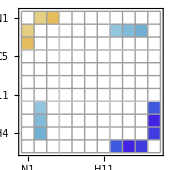
```mathematica
(*TO JEST BARDZO CENNE< NIE WYRZUCAJ TEGO!!!!
which={1,7,8,5,9,10,11,2,3,4,6};
elements={1,7,8,5,9,10,11,2,3,4,6};
MatrixPlot[mat⟦elements,elements⟧,FrameTicks->{{Range[Length[ATOMS[[which]]]],ATOMS[[which]]}ᵀ,{Range[Length[ATOMS[[which]]]],ATOMS[[which]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],Mesh->All,GridLines->{{3,7},{4,8}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True}]
-Graphics-
TO JEST BARDZO CENNE< NIE WYRZUCAJ TEGO!!!!*)
```

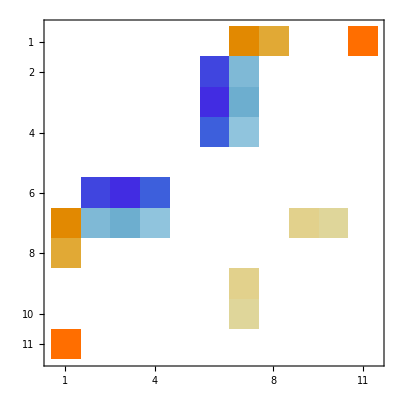

{0.95877,{1,-1,-1,-1,-1,1,1,1,1,1}}

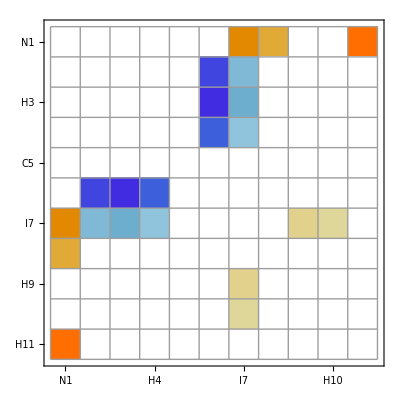

myMatrixPlotWithNumbers[{{0.,0.,0.,0.,0.,-1.17717,-0.799707,0.,0.,-1.76047},{0.,0.,0.,0.,1.36814,0.0585513,0.,0.,0.,0.},{0.,0.,0.,0.,1.37584,0.0595368,0.,0.,0.,0.},{0.,0.,0.,0.,1.35594,0.0582224,0.,0.,0.,0.},{0.,1.36814,1.37584,1.35594,0.,0.,0.,0.,0.,0.},{-1.17717,0.0585513,0.0595368,0.0582224,0.,0.,0.,-0.00706402,-0.00140173,0.},{-0.799707,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.00706402,0.,0.,0.,0.},{0.,0.,0.,0.,0.,-0.00140173,0.,0.,0.,0.},{-1.76047,0.,0.,0.,0.,0.,0.,0.,0.,0.}},{1,2,3,4,5,6,7,8,9,10}]

```mathematica
textSize=20;

interaction="non-bonded";
max="-62.50";
min="-172.50";
{angles,mats,varMats,diff}=getMatsFromInterval[max,min,interaction];
{mat,varMat}=meanForInterval[mats,varMats,diff];
MatrixPlot[mat]

{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200]

(*{whichLeft,whichRight}=Flatten[Position[myResults⟦2⟧,#]]&/@{1,-1}
0.5*Total[Total[packedMat⟦whichLeft,whichLeft⟧]]
0.5*Total[Total[packedMat⟦whichRight,whichRight⟧]]
Total[Total[packedMat⟦whichLeft,whichRight⟧]]
plotBlockLikeSimMat[myResults⟦2⟧,packedMat]
score1[myResults⟦2⟧,myResults⟦2⟧]*)
myMatrixPlot[mat,Range[Length[mat]],textSize]
myMatrixPlotWithNumbers[-packedMat,Range[Length[packedMat]],textSize]
```

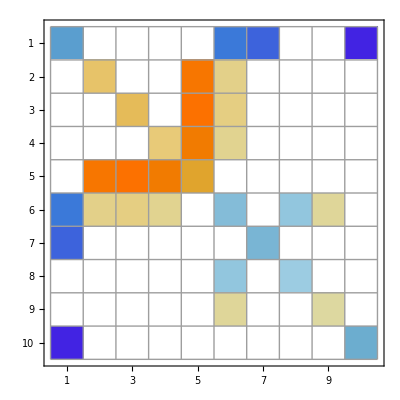

```mathematica
myMatrixPlotWithNumbers[-packedMat+DiagonalMatrix[Mean/@-packedMat],Range[Length[packedMat]],textSize]
```

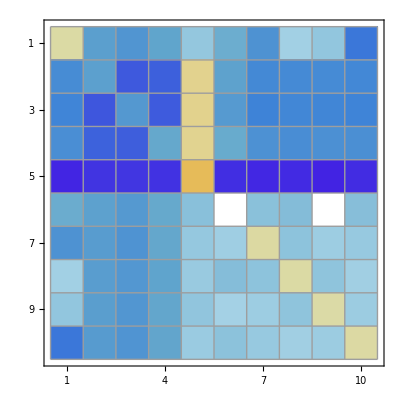

```mathematica
myMatrixPlotWithNumbers[Total@affinityPropagation2andAHalf[-packedMat,0.5,2],Range[Length[mat]],textSize]
```

```mathematica
interaction="tors";
prefix="tors";
{mats,accumulatedMat}=extractAccumulatedMat[max,min,interaction];
mat=accumulatedMat⟦All,All,1,-1⟧;
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200];
unpackedClustering=unpackClustering[myResults⟦2⟧,which,Length[mat]];
```

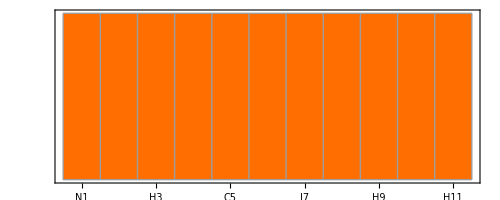

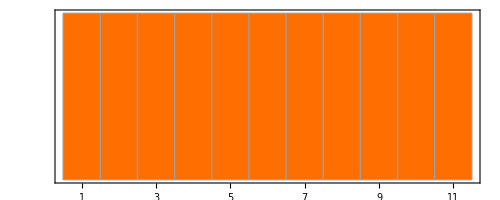

```mathematica
{reverseGear,forwardGear}=Flatten[Position[unpackedClustering,#]]&/@{-1,1};
MatrixPlot[{unpackedClustering},FrameTicks->{None,{Range[Length[ATOMS]],ATOMS}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,16],Mesh->True]
MatrixPlot[{unpackedClustering},FrameTicks->{None,{Range[Length[ATOMS]],NUMBERS}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,16],Mesh->True]
```

Transpose::nmtx: The first two levels of the one-dimensional list {{-179., -178.5, -178., -177.5, -177., -176.5, -176., -175.5, -175., -174.5, -174., -173.5, -173., -172.5, -172., -171.5, -171., -170.5, -170., -169.5, -169., -168.5, -168., -167.5, -167., -166.5, -166., -165.5, -165., -164.5, -164., -163.5, -163., -162.5, -162., -161.5, -161., -160.5, -160., -159.5, -159., -158.5, -158., -157.5, -157., -156.5, -156., -155.5, -155., -154.5, « 189 »}, {0.0696844, 0.0708086, 0.0785889, « 45 », 0.132225, 0.130972, « 171 »}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {{-179., -178.5, -178., -177.5, -177., -176.5, -176., -175.5, -175., -174.5, -174., -173.5, -173., -172.5, -172., -171.5, -171., -170.5, -170., -169.5, -169., -168.5, -168., -167.5, -167., -166.5, -166., -165.5, -165., -164.5, -164., -163.5, -163., -162.5, -162., -161.5, -161., -160.5, -160., -159.5, -159., -158.5, -158., -157.5, -157., -156.5, -156., -155.5, -155., -154.5, « 189 »}, {0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 23 », 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., 0., « 171 »}} cannot be transposed.

Transpose::nmtx: The first two levels of the one-dimensional list {{-179., -178.5, -178., -177.5, -177., -176.5, -176., -175.5, -175., -174.5, -174., -173.5, -173., -172.5, -172., -171.5, -171., -170.5, -170., -169.5, -169., -168.5, -168., -167.5, -167., -166.5, -166., -165.5, -165., -164.5, -164., -163.5, -163., -162.5, -162., -161.5, -161., -160.5, -160., -159.5, -159., -158.5, -158., -157.5, -157., -156.5, -156., -155.5, -155., -154.5, « 189 »}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, « 171 »}} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

-Graphics-

torsDerivative.pdf

Part::partw: Part 222 of {0., 0.0351232, 0.0724726, 0.11173, 0.151623, 0.192675, 0.234753, 0.277437, 0.320965, 0.366737, 0.41349, 0.460712, 0.508746, « 25 », 2.0876, 2.15571, 2.22367, 2.29062, 2.35921, 2.42627, 2.49213, 2.55816, 2.62346, 2.68833, 2.75326, 2.81906, « 171 »} does not exist.

Part::partw: Part 222 of {0., 1.35974×10^-7, 2.67809×10^-7, 3.92872×10^-7, 5.10384×10^-7, 6.22706×10^-7, 7.51099×10^-7, 9.01194×10^-7, 1.05788×10^-6, 1.21018×10^-6, 1.34621×10^-6, 1.47052×10^-6, 1.60623×10^-6, « 25 », 5.30492×10^-6, 5.43906×10^-6, 5.58015×10^-6, 5.73723×10^-6, 5.88191×10^-6, 6.0236×10^-6, 6.15792×10^-6, 6.2737×10^-6, 6.39084×10^-6, 6.51348×10^-6, 6.63648×10^-6, 6.75957×10^-6, « 171 »} does not exist.

Part::partw: Part 223 of {0., 0.0351232, 0.0724726, 0.11173, 0.151623, 0.192675, 0.234753, 0.277437, 0.320965, 0.366737, 0.41349, 0.460712, 0.508746, « 25 », 2.0876, 2.15571, 2.22367, 2.29062, 2.35921, 2.42627, 2.49213, 2.55816, 2.62346, 2.68833, 2.75326, 2.81906, « 171 »} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

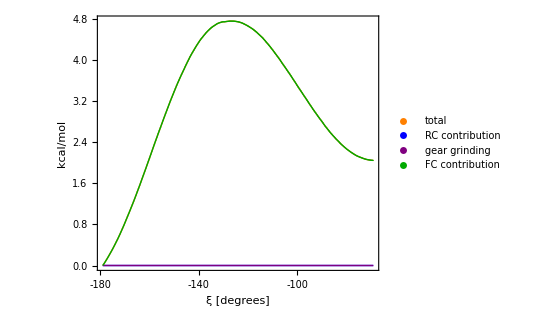

torsPMF.pdf

```mathematica
textSize=20;
{forwardPull,reversePull,gearGrinding,totalPull}=extractGearPMF[mats,forwardGear,reverseGear];

upperLimit=Max[Flatten[{forwardPull⟦1,All⟧,reversePull⟦1,All⟧,gearGrinding⟦1,All⟧}]];
lowerLimit=Min[Flatten[{forwardPull⟦1,All⟧,reversePull⟦1,All⟧,gearGrinding⟦1,All⟧}]];
step=(upperLimit-lowerLimit)/4;
ticks=Range[lowerLimit-step,upperLimit+step,step];
ListPlot[{{Range[-179,-60,0.5],forwardPull⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],reversePull⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],gearGrinding⟦1,All⟧}ᵀ,{Range[-179,-60,0.5],totalPull⟦1,All⟧}ᵀ},PlotLegends->Placed[PointLegend[{Style["FGC",Bold,textSize],Style["RGC",Bold,textSize],Style["GG",Bold,textSize],Style["total",Bold,textSize]},LegendMarkerSize->16,LegendMarkers->"Filled"],Above],Joined->True,PlotRange->All,PlotStyle->Thick,Frame->{{True,False},{True,False}},FrameLabel->{Style["ξ [degrees]",Bold,textSize],Style["kcal/mol",textSize,Bold]},FrameTicks->{{Automatic,None},{{-180,-160,-140,-120,-100,-80,-60},None}},LabelStyle->Directive[Black,textSize-2,Bold],AspectRatio->0.8]
Export[prefix<>"Derivative.pdf",%,"PDF"]

{forwardPull,reversePull,gearGrinding,totalPull}=extractGearPMF[accumulatedMat,forwardGear,reverseGear];
ErrorListPlot[prepareForErrorListPlot/@{forwardPull,reversePull,gearGrinding,totalPull},PlotLegends->Placed[PointLegend[{Style["total",Bold,textSize],Style["RC contribution",Bold,textSize],Style["gear grinding",Bold,textSize],Style["FC contribution",Bold,textSize]},LegendMarkerSize->16,LegendMarkers->"Filled"],Above],Joined->True,PlotRange->All,Frame->{{True,False},{True,False}},FrameLabel->{Style["ξ [degrees]",Bold,textSize],Style["kcal/mol",textSize,Bold]},PlotStyle->{Orange,Blue,Purple,Darker[Green]},FrameTicks->{{Automatic,None},{{-180,-160,-140,-120,-100,-80,-60},None}},LabelStyle->Directive[Black,textSize-2,Bold],AspectRatio->0.8]
Export[prefix<>"PMF.pdf",%,"PDF"]
```

```mathematica
textSize=20;


ListPlot[{ToExpression/@DIHEDRALS,Table[clusteringSimilarity[unpackedClustering,wyniki⟦All,2⟧⟦i⟧,Length[ATOMS]],{i,1,Length[wyniki⟦All,2⟧]}]}ᵀ,Joined->True,Frame->True,FrameLabel->{Style["ξ [degrees]",Bold,textSize],Style["SIMILARITY",textSize,Bold]},LabelStyle->Directive[Black,textSize-2,Bold],PlotStyle->Thick,PlotRange->{All,{-1,1}},Filling->Bottom]
```

-Graphics-

{0.413187,{1,1,1,1,1,1,1,1,1,1,1}}

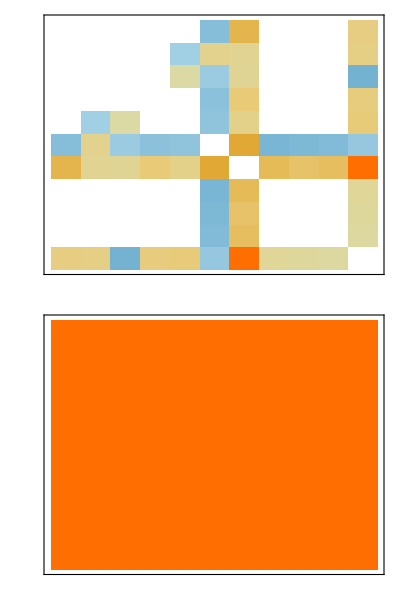

```mathematica
mat=accumulatedMat⟦All,All,1,-1⟧;
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200]
unpackedClustering=unpackClustering[myResults⟦2⟧,which,Length[mat]];
{reverseGear,forwardGear}=Flatten[Position[unpackedClustering,#]]&/@{-1,1};
plotBlockLikeSimMat[unpackedClustering+2,mat,72*3]
```

```mathematica
interaction="ele";
prefix="ele";
{mats,accumulatedMat}=extractAccumulatedMat[max,min,interaction];
mat=accumulatedMat⟦All,All,1,-1⟧;
{packedMat,which}=packMatrix[mat];
myResults=geneticClustering[packedMat,10,200];
unpackedClustering=unpackClustering[myResults⟦2⟧,which,Length[mat]];
```

{9,6,4,3,2,5,11,10,8,7,1}

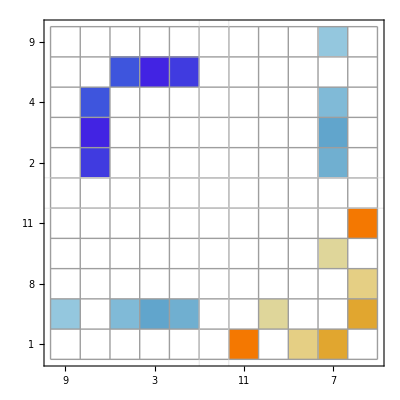

```mathematica
map=Sort[Range[1,Length[mat]],unpackedClustering[[#1]]<unpackedClustering[[#2]]&]
If[Length[Flatten[Position[unpackedClustering,0]]]==0,
zeroLeftPosition=Min[Flatten[Position[unpackedClustering⟦map⟧,1]]];
MatrixPlot[mat⟦map,map⟧,FrameTicks->{{Range[Length[ATOMS[[map]]]],ATOMS[[map]]}ᵀ,{Range[Length[ATOMS[[map]]]],Rotate[#,90 Degree]&/@ATOMS[[map]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,16],Mesh->All,GridLines->{{zeroLeftPosition-1},{Length[ATOMS]-zeroLeftPosition+1}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True}]
,
{zeroLeftPosition,zeroRightPosition}=#[Flatten[Position[unpackedClustering,0]]]&/@{Min,Max};
{zeroLeftPosition,zeroRightPosition}={zeroLeftPosition,zeroRightPosition}+1;
MatrixPlot[mat⟦map,map⟧,FrameTicks->{{Range[Length[ATOMS[[map]]]],NUMBERS[[map]]}ᵀ,{Range[Length[ATOMS[[map]]]],Rotate[#,0 Degree]&/@NUMBERS[[map]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Directive[Opacity[1],Bold,Black,16],Mesh->All,GridLines->{{zeroLeftPosition-1,zeroRightPosition},{Length[ATOMS]-zeroLeftPosition+1,Length[ATOMS]-zeroRightPosition}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True}]
]

(*,FrameTicks->{{Range[Length[ATOMS[[map]]]],ATOMS[[map]]}ᵀ,{Range[Length[ATOMS[[map]]]],ATOMS[[map]]}ᵀ},FrameStyle->Opacity[0],FrameTicksStyle->Opacity[1],Mesh->All,GridLines->{{3,7},{4,8}},GridLinesStyle->{Directive[Thick,Black],Directive[Thick,Black]},Method->{"GridLinesInFront"->True}]*)
```

```mathematica
max="-60.00";
min="-179.00";
freeEnergy=extractPMF[max,min,1]ᵀ;
freeEnergy={freeEnergy⟦1⟧,#^2&/@freeEnergy⟦2⟧};
entropy=extractPMF[max,min,3]ᵀ;
entropy={entropy⟦1⟧,#^2&/@entropy⟦2⟧};
energy={freeEnergy⟦1⟧-entropy⟦1⟧,freeEnergy⟦2⟧+entropy⟦2⟧};
```

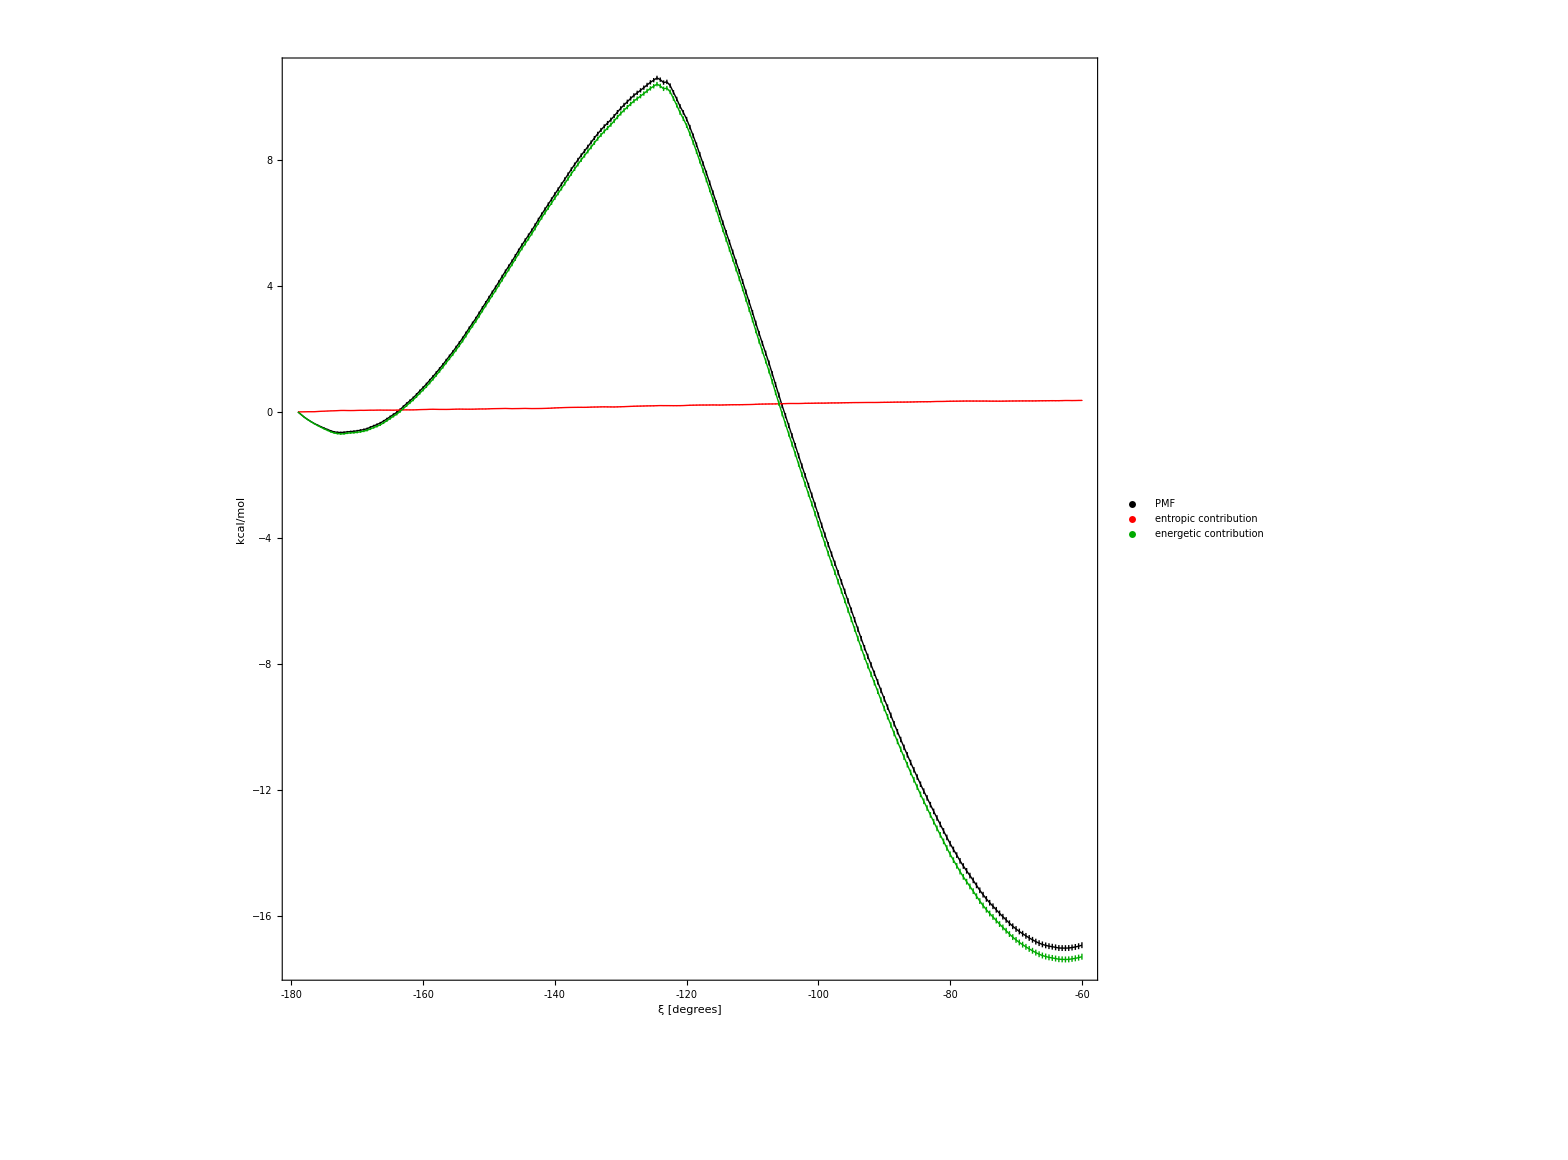

```mathematica
textSize=20;
g=ErrorListPlot[prepareForErrorListPlot[trapezoidalIntegration[#,0.5]]&/@{freeEnergy,entropy,energy},PlotLegends->Placed[PointLegend[{Style["PMF",Bold,textSize-6,FontFamily->"Helvetica"],Style["entropic\ncontribution",Bold,textSize-6,FontFamily->"Helvetica"],Style["energetic\ncontribution",Bold,textSize-6,FontFamily->"Helvetica"]},LegendMarkerSize->textSize-6,LegendMarkers->"Filled",LegendLayout->"Row"],Top],Joined->True,PlotRange->All,PlotStyle->{Black,Red,Darker[Green]},Frame->{{True,False},{True,False}},FrameLabel->{Style["ξ [degrees]",Bold,textSize,FontFamily->"Helvetica"],Style["kcal/mol",textSize,Bold,FontFamily->"Helvetica"]},FrameTicks->{{Automatic,None},{{-180,-160,-140,-120,-100,-80,-60},None}},LabelStyle->Directive[Black,textSize-6,Bold],TicksStyle->Directive[Bold,FontFamily->"Helvetica",textSize-6],AspectRatio->.9,ImageSize->72*4.5]
Export["realPMF.eps",%,"EPS"];
```

```mathematica
a=Import["angle-150_measured_1450x2000.png","PNG"];
b=Import["angle-90_measured_1550x2000.png","PNG"];
c=Import["angle-60_measured_2100x1400.png","PNG"];
(*{a,b,c}=ImageCrop/@{a,b,c};*)
c=ImageCrop[c];
g=Import["realPMF.pdf","PDF"]⟦1⟧
```

{-Graphics-}

```mathematica
Export["grid.eps",GraphicsGrid[{{a,c},{b,g}},ImageSize->72*6.5],"EPS",ImageResolution->1200]
```

grid.eps

-Graphics-

```mathematica
grafik=Labeled[MatrixPlot[{{1,1,1,1,1,1,2,1,1,1,1}},ImageSize->72*4],"asd",Top,ImageSize->72*4];
Export["grafik.pdf",grafik,"PDF",ImageSize->72*4]
```

grafik.pdf